# Homework 2 Problem 2

In this problem we are asked to find values corresponding to constant ξ, γ, or ϕ along with the value of d and either prolate of spheroidal coordinates that correspond to the following.

## Part a

```mathematica
$Assumptions=ξ>0&&γ>0&&ϕ>0&&a>0&&b>0&&d>0;
```

Here we find constant coordinate values for a prolate spheroid defined by the equation
	
where a > b.

We know that for the prolate spheroid, we have the following coordinates

```mathematica
x=d ξ Sin[γ]Cos[ϕ];
y=d ξ Sin[γ]Sin[ϕ];
z=d Sqrt[1+ξ^2]Cos[γ];
```

So we should be able to now just solve for each coordinate of constant value.

```mathematica
eqn=(x^2+y^2)/b^2+z^2/a^2==1;
```

Okay so now we can try and solve for ξ

```mathematica
eqn
```

(d^2 (1+ξ^2) Cos[γ]^2)/a^2+(d^2 ξ^2 Cos[ϕ]^2 Sin[γ]^2+d^2 ξ^2 Sin[γ]^2 Sin[ϕ]^2)/b^2==1

```mathematica
FullSimplify[PowerExpand[Solve[eqn,ξ]]]
```

{{ξ→ConditionalExpression[(b √(-2 a^2+d^2+d^2 Cos[2 γ]))/(d √(-a^2-b^2+(a-b) (a+b) Cos[2 γ])), ]}}

And we can also find that the variable d is given as

```mathematica
FullSimplify[PowerExpand[Solve[eqn,d]]]
```

{{d→(√2 a b)/(√(b^2+(a^2+b^2) ξ^2+(b^2+(-a+b) (a+b) ξ^2) Cos[2 γ]))}}

Great, now moving onto part b

## Part b

Here we want to find lines of constant coordinates relating to a plane with a circular hole of radius a. We can define a general equation or inequality as follows.

Below is a plot of the region for the case of a=0.3, just for intuitions sake.

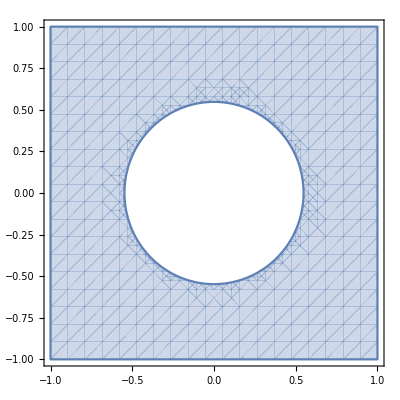

```mathematica
RegionPlot[p^2+m^2>0.3,{p,-1,1},{m,-1,1}]
```

So now we can do just as before, setup and equation and solve.

```mathematica
eqn1=x^2+y^2>=a
Reduce[Solve[eqn1,ξ]]
```

d^2 ξ^2 Cos[ϕ]^2 Sin[γ]^2+d^2 ξ^2 Sin[γ]^2 Sin[ϕ]^2≥a

Mathematic won’t solve this one for whatever reason but it’s pretty easy to see that in this case

and also

## Part c

Now we tackle the oblate cases so we need to clear our coordinates

```mathematica
Clear[x,y,z]
x = d Sqrt[1 + ξ^2] Sin[γ] Cos[ϕ];
y = d Sqrt[1 + ξ^2] Sin[γ] Sin[ϕ];
z = d ξ Cos[γ];
```

The equation we get constant values of ξ against is

```mathematica
FullSimplify[PowerExpand[Solve[(x^2+y^2)/a^2+z^2/b^2==1,ξ]]]
```

{{ξ→-(√(2 a^2-d^2+d^2 Cos[2 γ]))/(√((d^2 (a^2+b^2+(a-b) (a+b) Cos[2 γ]))/b^2))},{ξ→(√(2 a^2-d^2+d^2 Cos[2 γ]))/(√((d^2 (a^2+b^2+(a-b) (a+b) Cos[2 γ]))/b^2))}}

Where we take either result to be true but obvious preference for the positive valued ξ. The variable d then becomes

```mathematica
FullSimplify[PowerExpand[Solve[(x^2+y^2)/a^2+z^2/b^2==1,d]]]
```

{{d→-(√2)/(√((b^2+(a^2+b^2) ξ^2-(b^2+(-a+b) (a+b) ξ^2) Cos[2 γ])/(a^2 b^2)))},{d→(√2)/(√((b^2+(a^2+b^2) ξ^2-(b^2+(-a+b) (a+b) ξ^2) Cos[2 γ])/(a^2 b^2)))}}

## Part d

Now we consider a disk of radius a using the same coordinates

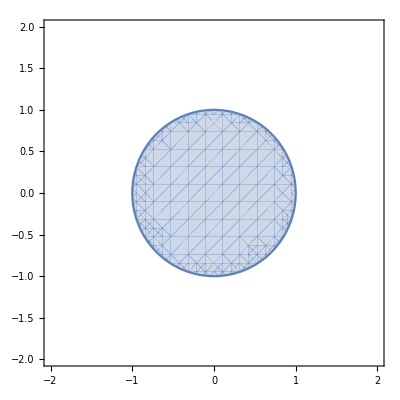

```mathematica
RegionPlot[m^2+p^2<1,{m,-2,2},{p,-2,2}]
```

So we set this up against the equation

```mathematica
x^2+y^2<a
```

d^2 (1+ξ^2) Cos[ϕ]^2 Sin[γ]^2+d^2 (1+ξ^2) Sin[γ]^2 Sin[ϕ]^2<a

Okay great so mathematica still doesn’t like this but it is pretty clear the inequality will obey the same exact general relationship, just with a slight change due to the coordinates being slightly different. We find

ξ =  and for d we find